# Electrokinetic thrusters for Lablet locomotion

Abhishek Sharma, John McCaskill
BioMIP
Ruhr Universität, Bochum,
Germany

## Calculation of surface charge and ζ potential on Silica surface

Here, we calculate the surface charge and ζ potential of Silica surface in the presence of aqueous electrolyte.

Calculation of surface charge densities and ζ potential is based on : 

1)  Sven H. Behrens and David G. Grier, The charge on Glass and Silica surfaces, J. Chem. Phys. 115, 6716 (2001)

2) Brian Kirby, Micro- and Nano Scale Fluid Mechanics, Transport in microfluidic devices

In the presence of electrolyte Silica surface acquires negative charge, due to the dissociation of Silanol groups
                                     
                                                            SiOH⇌SiO^-+H^+
                                                            
Using the Basic Stern model, charge on the surface comes from the  concentration Γ_(SiO^-) of dissociated head groups, which is equivalent to the fraction of total concentration : 

                                                            Γ=Γ_(SiO^-)+Γ_SiOH     
 
Note : Dimensions of  Γ is  m^-2.
 
And, the surface charge density is given by :                                                           
 
                                                             σ=-e Γ_(SiO^-) 
 
 Using the mass action law, 
                                                            ([H^+]_0 Γ_(SiO^-))/Γ_SiOH=10^-pK
                                                                                        
 where the concentration of the protons on the surface wrt. to bulk is given by the relation :                                                         
 
                                                            [H^+]_0=[H^+]_b exp(-β e ψ_0)
                                                            
                                                            [H^+]_b=10^-pH

   The linear potential drop from the Stern Layer is given by :
   
                                                             C=σ/(ψ_0-ψ_d)          
                                                             
 So, using these equations, we calculate the diffuse layer potential as a function of charge density,

```mathematica
eq1 = Γ== ΓSiO+ΓSiOH;
```

```mathematica
eq2=σ== -e ΓSiO;
```

```mathematica
eq3= (H0 ΓSiO)/ΓSiOH== 10^-pK;
```

```mathematica
eq4= H0== Hb Exp[-β e ψ0];
```

```mathematica
eq5= Hb== 10^-pH;
```

```mathematica
eq6= 𝒞== σ/(ψ0-ψd);
```

```mathematica
eq=Eliminate[{eq1&&eq2&&eq3&&eq4&&eq5&&eq6},{ΓSiOH,ΓSiO,H0,Hb,ψ0}]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

𝒞 Log[-(10^(-pH+pK) σ)/(e Γ+σ)]==e β (σ+𝒞 ψd)

```mathematica
sol=Solve[eq,ψd]//Flatten
```

{ψd→(-e β σ+𝒞 Log[-(10^(-pH+pK) σ)/(e Γ+σ)])/(e 𝒞 β)}

```mathematica
ψd/.sol
```

(-e β σ+𝒞 Log[-(10^(-pH+pK) σ)/(e Γ+σ)])/(e 𝒞 β)

Using Grahame’s equation (for a flat surface), 

                  σ(ψ_d)=(2ϵ ϵ_0 κ)/(β e)sinh((β e ψ_d)/2)
                  
and ψ_d calculated from the above treatment, could be used for estimating charge and potential of diffuse layer self consistently, using numerical methods.

```mathematica
{sol/.Rule-> Equal,σ== (2 ϵ ϵ0 κ)/(β e)Sinh[(β e ψd)/2]}//Flatten
```

{ψd==(-e β σ+𝒞 Log[-(10^(-pH+pK) σ)/(e Γ+σ)])/(e 𝒞 β),σ==(2 ϵ ϵ0 κ Sinh[(e β ψd)/2])/(e β)}

#### Physical constants

```mathematica
e=UnitConvert[Quantity["ElectronCharge"]];
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]];
```

```mathematica
T=Quantity[298.,"Kelvin"]; (* Temperature *)
```

```mathematica
ϵ0 = UnitConvert[Quantity["VacuumPermittivity"]];
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]];
```

```mathematica
β=1/(kB T);
```

#### Experimental parameters

```mathematica
z=1;(* Ionic Charge *)
```

```mathematica
ϵW=80;(* Dielectric Constant of water *)
```

```mathematica
ηW=Quantity[1 10^-3,"Kg/(m*s)"]; (* Viscosity of Water *)
```

```mathematica
cBulk= Quantity[1,"mol/m^3"]; (* Characteristic Bulk concentration *)
```

```mathematica
DebyeL[ϵ_,cB_,z_]:=√((ϵ ϵ0 kB T)/(2NA z^2 e^2 cB))
```

```mathematica
UnitConvert[DebyeL[ϵW,cBulk,1],"Meters"]
```

9.70886×10^-9 m

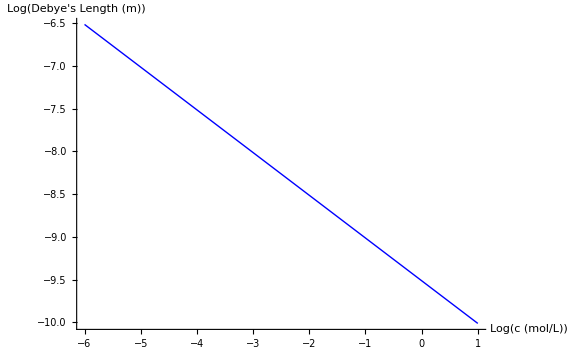

```mathematica
Plot[Evaluate[Log[10,DebyeL[ϵW,10^(x+3),1]/.q_Quantity:>QuantityMagnitude[q]]],{x,-6,1},PlotStyle-> {Blue, Thick},AxesLabel-> {"Log(c (mol/L))","Log(Debye's Length (m))"}]
```

```mathematica
UnitConvert[DebyeL[ϵW,cBulk,1],"Meters"]
```

9.70886×10^-9 m

```mathematica
𝒦=1/UnitConvert[DebyeL[ϵW,cBulk,1],"Meters"]
```

1.02999×10^8 per meter

```mathematica
κ[ϵ_,cB_,z_]:=1/DebyeL[ϵ, cB, z]
```

```mathematica
eA[ϵ_,cB_,z_]=σ== (2 ϵW ϵ0 κ[ϵ,cB,z])/(β e)Sinh[(β e ψd)/2] /.q_Quantity:>QuantityMagnitude[q]
```

σ==(0.0335146 Sinh[19.4707 ψd])/(√(ϵ/cB))

```mathematica
(* eA=σ== (2 ϵW ϵ0 κ)/(β e)Sinh[(β e ψd)/2] /.q_Quantity:>QuantityMagnitude[q]*)
```

```mathematica
eB[pH_,pK_,Γ_,𝒞_]=sol/.Rule-> Equal /.q_Quantity:>QuantityMagnitude[q]
```

{ψd==(0.0256797 (-38.9413 σ+𝒞 Log[-(10^(-pH+pK) σ)/((801088317 Γ)/5000000000000000000000000000+σ)]))/𝒞}

Here, Solve and NSolve are not able to find consistent solutions...so I use FindRoot

→ Typical values of various parameters are  :

    Γ = 8 nm^-2= 8 × 10^18 m^2, c_Bulk= 1 mol/m^-3, pk = 7.5, 𝒞=2.9 F/m^2

#### Effect of pH

Note : All the quantities used are in SI units, as pH is given by : -log(H^+), where [H^+] is in mol/lit. This means that pH and pK value need to be adjusted accordingly.

```mathematica
data=Table[Chop[FindRoot[{eA[80,1,z],eB[pH,7.5,8 10^18,2.9]⟦1⟧},{{ψd,0.001},{σ,0.001}}]],{pH,4,11,0.5}];
```

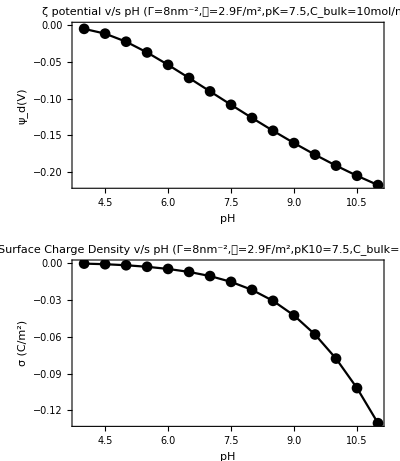

```mathematica
GraphicsColumn[{ListPlot[MapThread[{#1,#2}&,{Range[4,11,0.5],data⟦All,1,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "ζ potential v/s pH (Γ=8nm^-2,𝒞=2.9F/m^2,pK=7.5,C_bulk=10mol/m^3)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 9]},PlotTheme->"Monochrome",Frame-> True,FrameLabel-> {"pH","ψ_d(V)"}],ListPlot[MapThread[{#1,#2}&,{Range[4,11,0.5],data⟦All,2,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "Surface Charge Density v/s pH (Γ=8nm^-2,𝒞=2.9F/m^2,pK10=7.5,C_bulk=10mol/m^3)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->9]},PlotTheme->"Monochrome",Frame-> True,FrameLabel-> {"pH","σ (C/m^2)"}]},Frame-> All]
```

→ The reaction SiOH⇌SiO^-+H^+ suggests, Increase in pH causes more dissociation of Silanol groups, which increases surface charge and hence ζ potential. Assuming working pH is 8, hence ζ potential and surface charge density are given by  (We will use these as test values in further calculations ):

```mathematica
p1=ListPlot[MapThread[{#1,#2}&,{Range[4,11,0.5],data⟦All,1,2⟧}],Joined-> True,PlotMarkers-> Automatic,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotStyle->Blue,Frame-> True,FrameLabel-> {"pH","ψ_d(V)"},Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},ImagePadding->60];
```

```mathematica
p2=ListPlot[MapThread[{#1,#2}&,{Range[4,11,0.5],data⟦All,2,2⟧}],Joined-> True,PlotMarkers-> Automatic,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotStyle-> Red,Frame-> True,FrameLabel-> {{None,"σ (C/m^2)"},{None,"pH"}},Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Red},ImagePadding->60];
```

```mathematica
testVal=Chop[FindRoot[{eA[80,1,z],eB[10,7.5,8 10^18,2.9]⟦1⟧},{{ψd,0.1},{σ,0.1}}]]
```

{ψd→-0.191376,σ→-0.0777465}

```mathematica
{ζtest, σtest}={ψd, σ} /. testVal
```

{-0.191376,-0.0777465}

#### Effect of total concentration of Silanol groups (Γ)

```mathematica
data=Table[Chop[FindRoot[{eA[80,1,z],eB[10,7.5,i 10^18,2.9]⟦1⟧},{{ψd,0.1},{σ,0.1}}]],{i,1,10}];
```

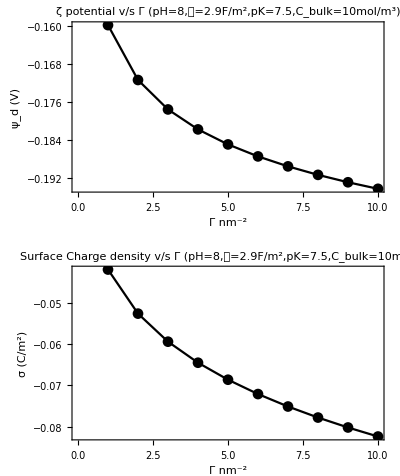

```mathematica
GraphicsColumn[{ListPlot[MapThread[{#1,#2}&,{Range[1,10],data⟦All,1,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "ζ potential v/s Γ (pH=8,𝒞=2.9F/m^2,pK=7.5,C_bulk=10mol/m^3)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 9]},PlotTheme->"Monochrome",Frame-> True,FrameLabel-> {"Γ nm^-2","ψ_d (V)"}],ListPlot[MapThread[{#1,#2}&,{Range[1,10],data⟦All,2,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "Surface Charge density v/s Γ (pH=8,𝒞=2.9F/m^2,pK=7.5,C_bulk=10mol/m^3)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 9]},PlotTheme->"Monochrome",Frame-> True,FrameLabel-> {"Γ nm^-2","σ (C/m^2)"}]},Frame-> All]
```

#### Effect of electrolyte concentration

```mathematica
data=Table[Chop[FindRoot[{eA[80,10^i,z],eB[10,7.5,8 10^18,2.9]⟦1⟧},{{ψd,0.1},{σ,0.1}}]],{i,-3,3,0.5}];
```

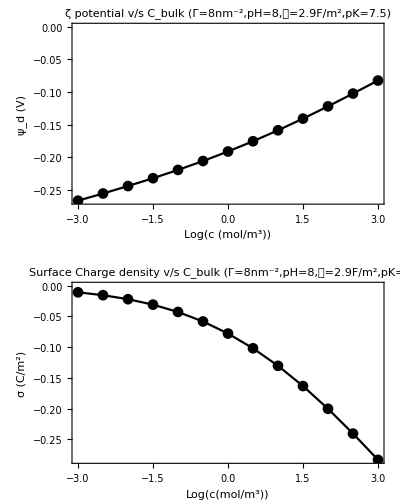

```mathematica
GraphicsColumn[{ListPlot[MapThread[{#1,#2}&,{Range[-3,3,0.5],data⟦All,1,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "ζ potential v/s C_bulk (Γ=8nm^-2,pH=8,𝒞=2.9F/m^2,pK=7.5)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->9]},PlotTheme->"Monochrome",Axes-> False,Frame-> True,FrameLabel-> {"Log(c (mol/m^3))","ψ_d (V)"}],ListPlot[MapThread[{#1,#2}&,{Range[-3,3,0.5],data⟦All,2,2⟧}],Joined-> True,PlotMarkers-> Automatic,PlotLabel-> "Surface Charge density v/s C_bulk (Γ=8nm^-2,pH=8,𝒞=2.9F/m^2,pK=7.5)",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->9]},PlotTheme->"Monochrome",Axes-> False,Frame-> True,FrameLabel-> {"Log(c(mol/m^3))","σ (C/m^2)"}]},Frame-> All]
```

## Simplified electrokinetic model (assuming Poisson Boltzmann Equilibrium)

In this formulation, we consider the system in equilibrium. So, the ion distribution is primarily governed by Poisson Boltzmann equation. Based, on these assumption we calculate by coupling with simplified Navier Stokes equation, electroosmotic thrust.  

The basic formulation is given in the following references : 

1)  D. Burgreen and F. R. Nakache, Electrokinetic Flow in Ultrafine Capillary Slits, J Phys. Chem. Volume 68, Number 6 May, 1964

2) Diez et al, On the capabilities of nano electrokinetic thrusters for space propulsion, Acta Astronautica 83 (2013) 97-107

The potential distribution inside the micro/nano channel assuming the double layer does not overlap with each other is given by :

h : height of microchannel
y : Position inside microchannel
ζ : zeta potential (from the last section)

```mathematica
hC=QuantityMagnitude@Quantity[1 10^-6,"m"];
wC=QuantityMagnitude@Quantity[20 10^-6,"m"];
```

Calculating ψ at single point, to check if the units are correct or not ...

```mathematica
κ[80.,cBulk,1]
```

1.02999×10^8 per meter

```mathematica
hTest=Quantity[1 10^-6,"m"];
```

```mathematica
yTest=Quantity[0.,"m"];
```

```mathematica
(4kB T)/e(ArcTanh[Tanh[(e ζtest)/(4kB T)]Exp[-κ[ϵW,cBulk,z] yTest]]+ArcTanh[Tanh[(e ζtest)/(4kB T)]Exp[-κ[ϵW,cBulk,z](hTest-yTest)]])
```

(ArcTanh[1.85454×10^-45 Tanh[-1.86311 s^3 A/(kg m^2)]]+ArcTanh[1. Tanh[-1.86311 s^3 A/(kg m^2)]]) (0.102719 kg m^2/(s^3 A))

As ζ potential and surface charge density also depends on bulk concentration, so to calculate the variation with concentration, we calculate ζ pot and surface charge density  :

So, we define the potential function at any point inside the channel :

```mathematica
ψ[h_,y_,ϵ_,cB_,z_,pH_]:=Module[{sol,ζ,σd,eBI},eBI=eB[pH,7.5,8 10^18,2.9];sol=Chop[FindRoot[{eA[ϵ,cB,z],eBI},{{ψd,0.01},{σ,0.01}}]];{ζ,σd}={ψd,σ}/.sol;
(4kB T)/e(ArcTanh[Tanh[(e ζ)/(4kB T)]Exp[-κ[ϵ,cB,z] y]]+ArcTanh[Tanh[(e ζ)/(4kB T)]Exp[-κ[ϵ,cB,z](h-y)]])/.q_Quantity:>QuantityMagnitude[q]]
```

```mathematica
p1=Plot[Evaluate[10^3 ψ[hC,y,ϵW,10^#,1,8]&/@{-3,-2,-1,0,1}],{y,0,hC},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},Frame-> True,FrameLabel->{"Distance (m)","ψ (mV)"},PlotRange-> Full,PlotStyle-> {Thick},PlotLegends-> {"10^-3mol/m^3","10^-2mol/m^3","10^-1mol/m^3","10^0mol/m^3","10^1mol/m^3"}];
```

```mathematica
ψN[h_,y_,ϵ_,cB_,z_,pH_]:=Module[{sol,ζ,σd,eBI},eBI=eB[pH,7.5,8 10^18,2.9];sol=Chop[FindRoot[{eA[ϵ,cB,z],eBI},{{ψd,0.001},{σ,0.001}}]];{ζ,σd}={ψd,σ}/.sol;
(4kB T)/e(ArcTanh[Tanh[(e ζ)/(4kB T)]Exp[-κ[ϵ,cB,z] y]]+ArcTanh[Tanh[(e ζ)/(4kB T)]Exp[-κ[ϵ,cB,z](h-y)]])/.q_Quantity:>QuantityMagnitude[q]]
```

```mathematica
p2=Plot[Evaluate[10^3 ψN[hC,y,ϵW,1,1,#]&/@Range[6,12,2]],{y,0,hC},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},Frame-> True,FrameLabel->{"Distance (m)","ψ (mV)"},PlotRange-> Full,PlotStyle-> {Thick},PlotLegends-> {"6","8","10","12"}];
```

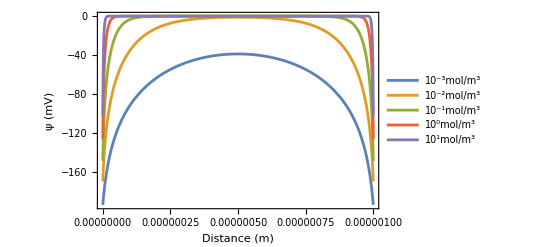

```mathematica
p1
```

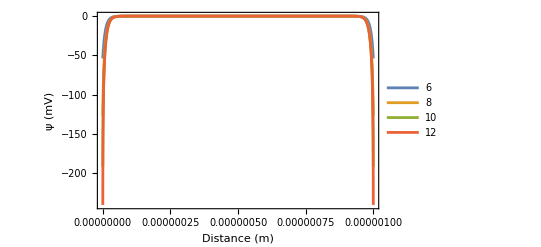

```mathematica
p2
```

#### Calculation of Electroosmotic flow velocity

The electric force which drives the fluid flow is given by : 

                                                                     F_z=E_z ϵ (∂^2 ψ)/(∂y^2)
                                                                     
The electroosmotic induced fluid flow is described by Navier Stokes equation (in the absence of external pressure), 

                                                                    η(ⅆ^2 v)/(ⅆ y^2)-E_z ϵ(ⅆ^2 ψ)/(ⅆ y^2)=0                                                                     
Navier’s slip boundary condition is given by : 
 
                                                                  v(±h/2)=-(ϵ ζ)/ηE_z[(1-ψ/ζ-b/ζ (-σ/ϵ))]                                                                  

Hence,  velocity profile across the channel is given by :

```mathematica
gap=60; (* Gap between electrodes *)
```

```mathematica
Vel[Ψ_,ζ_,σ_,ϵ_,η_,b_,Vapp_]:= -Vapp/(100 10^-6)(ϵ ϵ0 ζ)/η((1-Ψ/ζ)-b/ζ(-σ/(ϵ ϵ0)))
```

```mathematica
VelE[y_,h_,ϵ_,z_,cB_,η_,b_,pH_,Vapp_]:=Module[{sol,ζ,σd,eBI},sol=Chop[FindRoot[{eA[ϵ,cB,z],eB[pH,7.5,8 10^18,2.9]},{{ψd,0.01},{σ,0.01}}]];{ζ,σd}={ψd,σ}/.sol;
FullSimplify[Vel[ψ[h,y,ϵ,cB,z,pH],ζ,σd,ϵ,η,b,Vapp]/.q_Quantity:>QuantityMagnitude[q]]]
```

```mathematica
ηWMag=QuantityMagnitude@ηW; (* Magnitude of viscosity (without units) *)
```

```mathematica
b=Quantity[20 10^-9,"m"]; (* Slip length *)
```

```mathematica
bMag=QuantityMagnitude@b; (* Magnitude of slip length (without units) *)
```

```mathematica
ζtestU=Quantity[ζtest,"kg*m^2/Amperes/s^3"]; (* test ζ potential with units *)
```

```mathematica
σtestU=Quantity[σtest,"C/m^2"]; (* test surface charge density with units *)
```

```mathematica
cBtest=Quantity[100,"mol/m^3"];
```

```mathematica
cBtestMag=QuantityMagnitude@cBtest;
```

```mathematica
{ηWMag,bMag,cBtest,ζtestU,σtestU}//UnitSimplify//N
```

{0.001,2.×10^-8,100. mol/m^3,-0.191376 V,-0.0777465 C/m^2}

```mathematica
VelE[0,1 10^-6,ϵW,z,1,ηWMag,bMag,10,2]
```

0.0310986

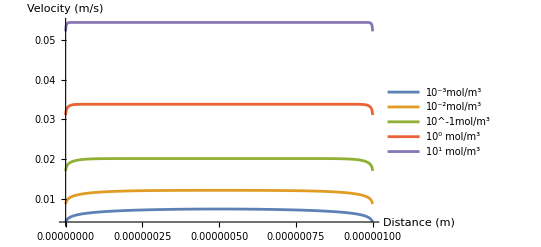

```mathematica
Plot[Evaluate[VelE[y,hC,ϵW,z,10^#,ηWMag,bMag,10,2]&/@{-3,-2,-1,0,1}],{y,0, 1 10^-6},AxesLabel-> {"Distance (m)","Velocity (m/s)"},PlotRange-> Full,PlotStyle-> {Thick},PlotLegends-> {"10^-3mol/m^3","10^-2mol/m^3","10^-1mol/m^3","10^0 mol/m^3","10^1 mol/m^3"}]
```

#### Calculation of current flowing

The current flowing in the system consists of two parts, conduction current and convection current. 
     The convection current is given by : 
                                                                                          j_conv= 2 e n_0 sinh((e ψ)/(k_B T))(e E_z ζ)/η((1-ψ/ζ)-b/ζ(-σ/ϵ))
     and, conduction current is given by :  
     
                                                                                          j_cond= μ e (n_+-n_-)E_z= 2μ e n_0 cosh((e ψ)/(k_B T))E_z

```mathematica
μ=Quantity[1 10^-9,"m^2/s"]/(kB T)
```

2.43053×10^11 s/kg

```mathematica
Eztest=Quantity[33333.,"V/m"];
```

```mathematica
jConv[Ψ_,Ez_,ζ_,σ_,cB_,b_,ϵ_,η_]:=2 NA e cB Sinh[(e Ψ)/(kB T)](ϵ ϵ0 Ez ζ)/η((1-Ψ/ζ)-b/ζ(-σ/(ϵ ϵ0)))
```

```mathematica
jConvE[y_,h_,Ez_,cB_,bx_,ϵ_,η_,z_,pH_]:=Module[{sol,ζ,σd},sol=Chop[FindRoot[{eA[ϵ,cB,z],eB[pH,7.5,8 10^18,2.9]},{{ψd,0.1},{σ,0.1}}]];{ζ,σd}={ψd,σ}/.sol;
jConv[ψ[h,y,ϵ,cB,z,pH],Ez,ζ,σd,cB,bx,ϵ,η]/.q_Quantity:>QuantityMagnitude[q]];
```

```mathematica
jCond[Ψ_,Ez_,cB_,μ_]:=2NA μ e Ez cB Cosh[(e Ψ)/(kB T)]/.q_Quantity:>QuantityMagnitude[q];
```

```mathematica
jCondE[y_,h_,ϵ_,Ez_,cB_,z_,η_]:=Module[{sol,ζ,σd},sol=Chop[FindRoot[{eA[ϵ,cB,z],eBI},{{ψd,0.1},{σ,0.1}}]];{ζ,σd}={ψd,σ}/.sol;jCond[ψ[h,y,ϵ,cB,z],Ez,cB,μ]/.q_Quantity:>QuantityMagnitude[q]];
```

```mathematica
(* jTot[y_,h_,ζ_,Ez_,cB_,σ_,b_,ϵ_,η_,z_]:=(jConvE[y,h,ζ,Ez,cB,σ,b,ϵ,η,z]+jCondE[y,h,ζ,ϵ,Ez,cB,z,η])/.q_Quantity:>QuantityMagnitude[q] *)
```

```mathematica
(* iTot[h_,ζ_,Ez_,cB_,σ_,b_,ϵ_,η_,z_]:=NIntegrate[jTot[y,h,ζ,Ez,cB,σ,b,ϵ,η,z],{y,0,h}]/.q_Quantity:>QuantityMagnitude[q] *)
```

#### Convection current

```mathematica
hC//N
```

1.×10^-6

```mathematica
NIntegrate[jConvE[y,hC,Eztest,10,bMag,ϵW,ηWMag,z,8],{y,0,hC}]20 10^-6
```

4.90342×10^-8

#### Conduction current

```mathematica
NIntegrate[jCond[ψ[hC,y,80,10,z,10],Eztest,cBulk,2.4 10^-11],{y,0,hC}]20 10^-6
```

3.46827×10^-12

## Calculation of electroosmotic thrust

The thrust is proportional to the exhaust velocity and mass flow rate, hence thrust is given by : 

                                                                   Th = ṁ v_m
     
        where, ṁ is the mass flow rate given by :     ṁ=ρ v_m h w                                                              
        
        Hence, it can be written as :             Th=ρ w (h((e E_z ζ)/η))^2(1/h∫(1-ψ/ζ)ⅆy -b/ζ(-σ/ϵ))^2

Checking the units  by using test values :

```mathematica
ρW = Quantity[1000,"Kg/m^3"];
```

```mathematica
ρWMag=QuantityMagnitude@ρW;
```

```mathematica
wC=Quantity[20 10^-6,"m"];
```

```mathematica
wCMag=QuantityMagnitude@wC;
```

```mathematica
hC=Quantity[1 10^-6,"m"];
```

```mathematica
hCMag=QuantityMagnitude@hC;
```

```mathematica
EOThrust[ρ_,w_,h_,Vapp_,η_,ϵ_,z_,cB_,pH_,bx_]:=Module[{sol,ζ,σd},sol=Chop[FindRoot[{eA[ϵ,cB,z],eB[pH,7.5,8 10^18,2.9]},{{ψd,0.0001},{σ,0.0001}}]];{ζ,σd}={ψd,σ}/.sol;
 (ρ w h (1/h NIntegrate[VelE[y,h,ϵ,z,cB,η,bx,pH,Vapp],{y,0,h}])^2)/.q_Quantity:>QuantityMagnitude[q]];
```

```mathematica
EOThrustMag=EOThrust[ρWMag,wCMag,1 10^-6,2,ηWMag,ϵW,z,10,10,bMag]
```

5.91057×10^-11

Plot of EO thrust v/s pH (at conc. 10 mol/m^3)

```mathematica
t1=Table[{pH,10^9 EOThrust[ρWMag,wCMag,1 10^-6,2,ηWMag,ϵW,z,10,pH,bMag]},{pH,6,10,0.5}];
```

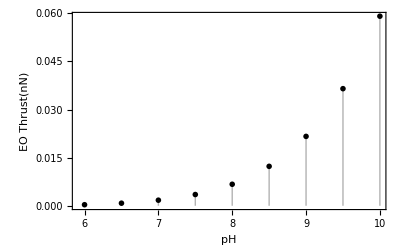

```mathematica
ListPlot[t1,Frame-> True,FrameLabel-> {"pH","EO Thrust(nN)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotTheme-> "Monochrome",Filling-> Axis]
```

```mathematica
EOThrust[ρ_,w_,h_,Vapp_,η_,ϵ_,z_,cB_,pH_,bx_]:=Module[{sol,ζ,σd},sol=Chop[FindRoot[{eA[ϵ,cB,z],eB[pH,7.5,8 10^18,2.9]},{{ψd,0.01},{σ,0.01}}]];{ζ,σd}={ψd,σ}/.sol;
 (ρ w h (1/h NIntegrate[VelE[y,h,ϵ,z,cB,η,bx,pH,Vapp],{y,0,h}])^2)/.q_Quantity:>QuantityMagnitude[q]];
```

Plot of EO thrust v/s Log(conc.(mol/m^3)) (at pH 10 )

```mathematica
t2=Table[{x,10^9 EOThrust[ρWMag,wCMag,1 10^-6,2,ηWMag,ϵW,z,10^x,8,bMag]},{x,-3,3,0.5}];
```

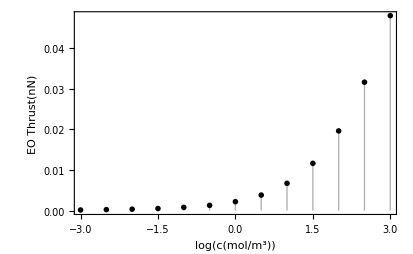

```mathematica
ListPlot[t2,Frame-> True,FrameLabel-> {"log(c(mol/m^3))","EO Thrust(nN)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotTheme-> "Monochrome",Filling-> Axis,Axes-> False]
```

### Calculation of velocity of Lablet

The lablet pairs (gemlabs) are 100x100x100 µm and can activate movement with electroosmotic thrust switching between three states:
(i) no thrust
(ii) right angle channel thrust
(iii) through channel thrust

The estimated achievable drift velocity under electroosmotic thrust of 2×10^-11N  is expected to be achieved almost instantaneously. We do the calculation in units of the diam i.e. 100 µm and seconds.

```mathematica
mode[t_]:=If[Mod[IntegerPart[2t],20]==0,1,If[Mod[IntegerPart[2t],20]==10,2,0]];
```

#### Linear diffusion and drift

First define viscosity η, the Boltzmann constant and room temperature 25°C

```mathematica
η=Quantity[0.798 10^-3,("Kilograms"/("Meters"*"Seconds"))]
```

0.000798 kg/(m s)

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]];
```

```mathematica
T=Quantity[298.,"Kelvins"]; (* Temperature *)
```

The linear friction coefficient is

```mathematica
frictioncoeff=6π η r/.r->Quantity[0.000050,"Meters"]
```

7.52097×10^-7 kg/s

```mathematica
thrust = UnitConvert[Quantity[EOThrustMag ,"Newtons"]]//N
```

5.91057×10^-11 kg m/s^2

```mathematica
driftvel=thrust/frictioncoeff
```

0.0000785878 m/s

```mathematica
UnitConvert[driftvel,"microns/s"]
```

78.5878 microns/s

```mathematica
Quantity[100 10^-6,"m"]/driftvel
```

1.27246 s

#### At constant conc. 10 mol/m^3

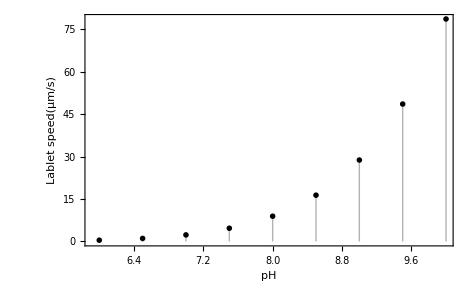

```mathematica
ListPlot[{#⟦1⟧,UnitConvert[Quantity[10^-9#⟦2⟧,"Newtons"]/frictioncoeff,"microns/s"]}&/@t1,Frame-> True,FrameLabel-> {"pH","Lablet speed(µm/s)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotTheme-> "Monochrome",Filling-> Axis]
```

#### At constant pH 8

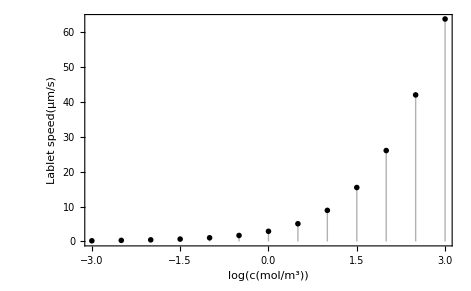

```mathematica
ListPlot[{#⟦1⟧,UnitConvert[Quantity[10^-9#⟦2⟧,"Newtons"]/frictioncoeff,"microns/s"]}&/@t2,Frame-> True,FrameLabel-> {"log(c(mol/m^3))","Lablet speed(µm/s)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotTheme-> "Monochrome",Filling-> Axis,Axes-> False]
```

#### Rotational diffusion and drift

Note that rotational diffusion can be essentially ignored, since it is given by

```mathematica
kB T/(8π η r^3)/.r->Quantity[0.000050,"Meters"]
```

1.64114×10^-6 per second

It will certainly be insignificant compared with settling hydrodynamic effects. This is much less than for a 1µm radius sphere in water, where the values are appreciable

```mathematica
kB T/(8π η r^3)/.r->Quantity[0.000001,"Meters"]
```

0.205143 per second

However, the driven rotation is significant

```mathematica
frictionangularforce=8π η r^3/.r->Quantity[0.000050,"Meters"]
```

2.50699×10^-15 kg m^2/s

the torque exerted by the electroosmotic thrust in mode 1 is approximately

```mathematica
torque=0.5thrust r /.r->Quantity[0.000050,"Meters"]
```

1.47764×10^-15 kg m^2/s^2

the resulting drift angular velocity is then

```mathematica
driftangvel=torque/frictionangularforce
```

0.589408 per second

translational velocity ≈ 70-80 µm/s, angular velocity ≈ 0.6 rad/s will be used in other files...!

#### Programmable motion of Lablets

Hence, in this file, we summarize the various parameters, which we will consider for the simulations in chemical fields.

→ Drift velocity : 70 µm/s

→ Rotational velocity : 0.6 rad/s

```mathematica
Clear[eqns]
```

```mathematica
eqns[t_,x_,y_,θ_,α_,v1_,ω1_]:={D[x[t],t]==Piecewise[{{2. Cos[θ[t]] v1,mode[t]==1},{v1 (Cos[θ[t]] (1+Sin[α])-Cos[α] Sin[θ[t]]),mode[t]==2}},0],
D[y[t],t]==Piecewise[{{2. Sin[θ[t]] v1,mode[t]==1},{v1 (Cos[α] Cos[θ[t]]+(1+Sin[α]) Sin[θ[t]]),mode[t]==2}},0],
D[θ[t],t]==Piecewise[{{ω1,mode[t]==2}},0],
x[0]==0.,y[0]==0.,θ[0]==0}
```

```mathematica
eqns[t,x,y,θ,α,v,ω]
```

{x'[t]==(Piecewise[{{2. v Cos[θ[t]], If[Mod[IntegerPart[2 t],20]==0,1,If[Mod[IntegerPart[2 t],20]==10,2,0]]==1}, {v (Cos[θ[t]] (1+Sin[α])-Cos[α] Sin[θ[t]]), If[Mod[IntegerPart[2 t],20]==0,1,If[Mod[IntegerPart[2 t],20]==10,2,0]]==2}, {0, True}}]),y'[t]==(Piecewise[{{2. v Sin[θ[t]], If[Mod[IntegerPart[2 t],20]==0,1,If[Mod[IntegerPart[2 t],20]==10,2,0]]==1}, {v (Cos[α] Cos[θ[t]]+(1+Sin[α]) Sin[θ[t]]), If[Mod[IntegerPart[2 t],20]==0,1,If[Mod[IntegerPart[2 t],20]==10,2,0]]==2}, {0, True}}]),θ'[t]==(Piecewise[{{ω, If[Mod[IntegerPart[2 t],20]==0,1,If[Mod[IntegerPart[2 t],20]==10,2,0]]==2}, {0, True}}]),x[0]==0.,y[0]==0.,θ[0]==0}

```mathematica
eqMode1={x'[t]==2 v Cos[θ[t]],y'[t]==2 v Sin[θ[t]],θ'[t]==0};
```

```mathematica
eqMode2={x'[t]==v (Cos[θ[t]] (1+Sin[α])-Cos[α] Sin[θ[t]]),y'[t]==v (Cos[α] Cos[θ[t]]+(1+Sin[α]) Sin[θ[t]]),θ'[t]==ω};
```

```mathematica
soln1=DSolve[eqMode1,{x[t],y[t],θ[t]},t]
```

{{θ[t]→C[1],x[t]→C[2]+2 t v Cos[C[1]],y[t]→C[3]+2 t v Sin[C[1]]}}

```mathematica
C1=First[Solve[(θ[t]/.soln1/.t-> 0)== θ0,C[1]]];
C2=First[Solve[(x[t]/.soln1/.t-> 0/.C[1]->θ0)== x0,C[2]]];
C3=First[Solve[(y[t]/.soln1/.t-> 0/.C[1]->θ0)== y0,C[3]]];
op1={x[t],y[t],θ[t] }/.soln1/.C1/.C2/.C3//First
```

{x0+2 t v Cos[θ0],y0+2 t v Sin[θ0],θ0}

```mathematica
soln2=DSolve[eqMode2,{x[t],y[t],θ[t]},t]
```

{{θ[t]→t ω+C[1],x[t]→C[2]+(v Cos[α] Cos[t ω] Cos[C[1]])/ω+(v Cos[C[1]] Sin[t ω])/ω+(v Cos[C[1]] Sin[α] Sin[t ω])/ω+(v Cos[t ω] Sin[C[1]])/ω+(v Cos[t ω] Sin[α] Sin[C[1]])/ω-(v Cos[α] Sin[t ω] Sin[C[1]])/ω,y[t]→C[3]-(v Cos[t ω] Cos[C[1]])/ω-(v Cos[t ω] Cos[C[1]] Sin[α])/ω+(v Cos[α] Cos[C[1]] Sin[t ω])/ω+(v Cos[α] Cos[t ω] Sin[C[1]])/ω+(v Sin[t ω] Sin[C[1]])/ω+(v Sin[α] Sin[t ω] Sin[C[1]])/ω}}

```mathematica
C1=First[Solve[(θ[t]/.soln2/.t-> 0)== θ0,C[1]]];
C2=First[Solve[(x[t]/.soln2/.t-> 0/.C[1]->θ0)== x0,C[2]]];
C3=First[Solve[(y[t]/.soln2/.t-> 0/.C[1]->θ0)== y0,C[3]]];
op2={x[t],y[t],θ[t] }/.soln2/.C1/.C2/.C3//First
```

{(v Cos[α] Cos[θ0] Cos[t ω])/ω+(v Cos[t ω] Sin[θ0])/ω+(v Cos[t ω] Sin[α] Sin[θ0])/ω+(x0 ω-v Cos[α] Cos[θ0]-v Sin[θ0]-v Sin[α] Sin[θ0])/ω+(v Cos[θ0] Sin[t ω])/ω+(v Cos[θ0] Sin[α] Sin[t ω])/ω-(v Cos[α] Sin[θ0] Sin[t ω])/ω,-(v Cos[θ0] Cos[t ω])/ω-(v Cos[θ0] Cos[t ω] Sin[α])/ω+(v Cos[α] Cos[t ω] Sin[θ0])/ω+(y0 ω+v Cos[θ0]+v Cos[θ0] Sin[α]-v Cos[α] Sin[θ0])/ω+(v Cos[α] Cos[θ0] Sin[t ω])/ω+(v Sin[θ0] Sin[t ω])/ω+(v Sin[α] Sin[θ0] Sin[t ω])/ω,θ0+t ω}

#### Defining parameters...

```mathematica
α=π/12;vLablet=70;ωLablet=0.6;
```

```mathematica
traj1[t_,{x0_,y0_,θ0_},{v_,ω_}]=op1;
```

```mathematica
traj2[t_,{x0_,y0_,θ0_},{v_,ω_}]=op2;
```

```mathematica
traj[op_,t_,{x0_,y0_,θ0_},{v_,ω_}]:= Which[op== 0,traj1[t,{x0,y0,θ0},{v,ω}],op== 1,traj2[t,{x0,y0,θ0},{v,ω}]]
```

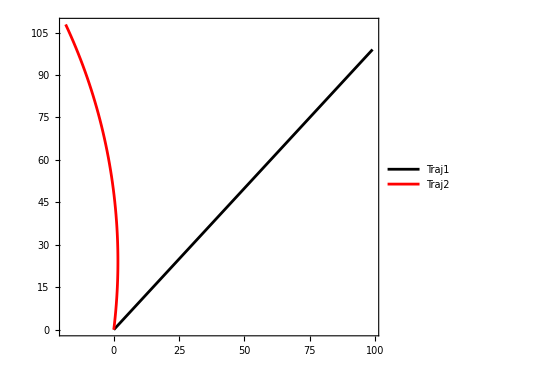

```mathematica
ParametricPlot[{traj[0,t,{0,0,π/4},{vLablet,ωLablet}]⟦1;;2⟧,traj[1,t,{0,0,π/4},{vLablet,ωLablet}]⟦1;;2⟧},{t,0,1},PlotStyle-> {{Black,Thick},{Red,Thick}},PlotLegends-> {"Traj1","Traj2"},Frame-> True,Axes-> None]
```

0 : Thrust operation 1,  1 : Thrust operation 2
Using a combination of various two thrust operations, we could create complex patterned motion of Lablets.

Assuming each operation of will be performed for fixed time. Hence, timing of operation will be defined by number of times its repeated in ThrustSeq.

```mathematica
plotTraj[ThrustSeq_,totTime_,Δt_,vL_,ωL_,color_]:=Module[{nSeq,nOp,pos,totSeq,X,Y,Θ,ns,cOp},
nSeq=Length[ThrustSeq];
nOp=(totTime/Δt);(* Number of switching operations *)
totSeq=Table[ThrustSeq,{nOp}]//Flatten;
X=0;Y=0;Θ=0;pos={{X,Y,Θ}};
ns=1;While[ns≤nOp,cOp=totSeq⟦ns⟧;{X,Y,Θ}=traj[cOp,t,{X,Y,Θ},{vL,ωL}]/.t-> Δt;pos=Join[pos,{{X,Y,Θ}}];ns++];
Show[{Table[ParametricPlot[Evaluate[traj[totSeq⟦i⟧,t,pos⟦i⟧,{vL,ωL}]⟦1;;2⟧],{t,0,Δt},PlotStyle-> color],{i,1,nOp}]},PlotRange-> All,Frame-> True,Axes-> None,FrameLabel-> {"X(µm)","Y (µm)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 10]}]]
```

#### 1. Cyclic motion

```mathematica
ThrustSeq1=Join[{0,0,1}];
```

```mathematica
ThrustSeq2=Join[{0,0,1,1}];
```

```mathematica
ThrustSeq3=Join[{0,0,1,1,1}];
```

```mathematica
p1=Show[{plotTraj[ThrustSeq1,25,0.1,vLablet,ωLablet,Blue],plotTraj[ThrustSeq2,20,0.05,vLablet,ωLablet,Red],plotTraj[ThrustSeq3,15,0.05,vLablet,ωLablet,Green]}];
```

```mathematica
p2=Show[{plotTraj[ThrustSeq1,25,0.2,vLablet,ωLablet,Blue],plotTraj[ThrustSeq2,20,0.1,vLablet,ωLablet,Red],plotTraj[ThrustSeq3,15,0.1,vLablet,ωLablet,Green]}];
```

```mathematica
p3=Show[{plotTraj[ThrustSeq1,25,0.5,vLablet,ωLablet,Blue],plotTraj[ThrustSeq2,20,0.3,vLablet,ωLablet,Red],plotTraj[ThrustSeq3,15,0.3,vLablet,ωLablet,Green]}];
```

Same sequence with different frequency of switching.... {0.5, 0.1, 0.3}

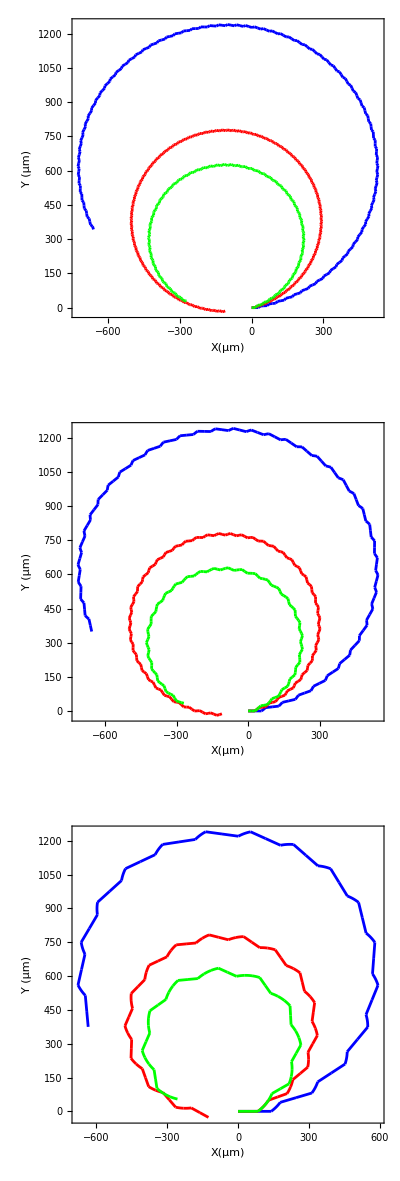

```mathematica
GraphicsColumn[{p1,p2,p3},Frame-> All]
```

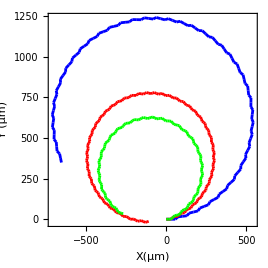

```mathematica
p2
```

#### 2. Random sequence of operations

Here, we define a random sequence, and periodically repeating multiple times (the length of sequence depends on number of memory bits available on Lablet)

```mathematica
ThrustSeq=Table[RandomInteger[],{8}]
```

{0,0,1,1,1,1,0,1}

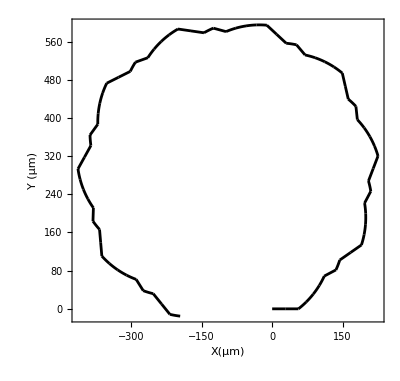

```mathematica
p2x=plotTraj[ThrustSeq,15,0.2,vLablet,ωLablet,Black]
```

#### 3. Cylic motion with drift

```mathematica
ThrustSeq1=Join[ConstantArray[Join[{0,0,1,1}],25],{1,1,1,1}]//Flatten;
```

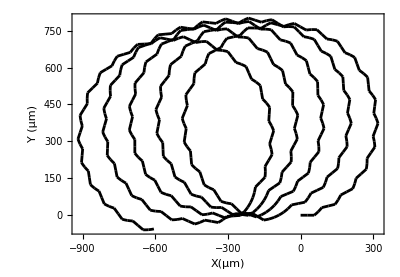

```mathematica
p3x=plotTraj[ThrustSeq1,100,0.2,vLablet,ωLablet,Black]
```

```mathematica
ThrustSeq4=Join[{ConstantArray[0,50]},ConstantArray[1,20],ConstantArray[0,50],ConstantArray[1,35]]//Flatten;
```

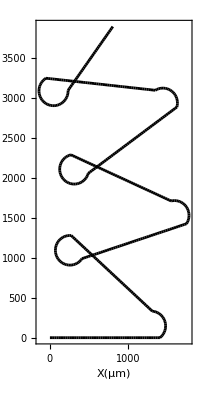

```mathematica
p4=plotTraj[ThrustSeq4,100,0.2,vLablet,ωLablet,Black]
```

So, plotting these different trajectories together

```mathematica
GraphicsGrid[Partition[{p2,p2x,p3x,p4},2],Frame-> All]
```

-Graphics-

```mathematica
plotTraj[ThrustSeq_,totTime_,Δt_,vL_,ωL_,color_]:=Module[{nSeq,nOp,pos,totSeq,X,Y,Θ,ns,cOp},
nSeq=Length[ThrustSeq];
nOp=(totTime/Δt);(* Number of switching operations *)
totSeq=Table[ThrustSeq,{nOp}]//Flatten;
X=0;Y=0;Θ=π/6;pos={{X,Y,Θ}};
ns=1;While[ns≤nOp,cOp=totSeq⟦ns⟧;{X,Y,Θ}=traj[cOp,t,{X,Y,Θ},{vL,ωL}]/.t-> Δt;pos=Join[pos,{{X,Y,Θ}}];ns++];
Show[{Table[ParametricPlot[10^-3 Evaluate[traj[totSeq⟦i⟧,t,pos⟦i⟧,{vL,ωL}]⟦1;;2⟧],{t,0,Δt},PlotStyle-> color],{i,1,nOp}]},PlotRange-> All,Frame-> True,Axes-> None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 10]}]]
```

```mathematica
ThrustSeqA=Table[IntegerDigits[k,2,5],{k,0,31}]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
pa=GraphicsGrid[Partition[Table[plotTraj[ThrustSeqA⟦k⟧,10,3,vLablet,ωLablet,Blue],{k,32}],8]];
```

You need to evaluate above line : large file.

```mathematica
{vLablet,ωLablet}
```

{70,0.6}

#### changed dimensions to mm and changed starting angle from 0 to π/6, so that its easy to visualize first plot.

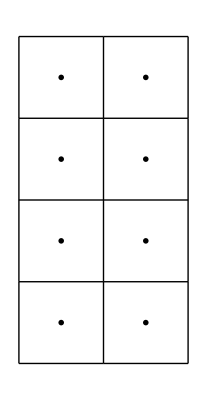

```mathematica
pa=GraphicsGrid[Partition[Table[plotTraj[ThrustSeqA[[k]],500,3,vLablet,ωLablet,Black],{k,1+{0,1,3,5,7,11,15,31}}],2],Frame-> All]
```

#### Similarly plotting 4 bit...

```mathematica
ThrustSeqB=Table[IntegerDigits[k,2,4],{k,0,15}]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

```mathematica
pa=GraphicsGrid[Partition[Table[plotTraj[ThrustSeqB[[k]],300,3,vLablet,ωLablet,Black],{k,1+{0,1,3,5,7,15}}],3],Frame-> All]
```

-Graphics-